# lens design

P.Huft

```mathematica
SetDirectory[NotebookDirectory[]];
<<"optics.m"
SetOptions[Plot,Axes->False,Frame->{True,True,False,False},LabelStyle->Directive[Black, 16],ImageSize->Medium];
SetOptions[ListPlot,Axes->False,Frame->{True,True,False,False},LabelStyle->Directive[Black, 16],ImageSize->Medium];
```

## singlet

can we correct correct a focal shift from one singlet lens with another singlet lens?
Consider a lens which is weaker for λ2 than λ1, where λ2 > λ1 because n(λ2) < n(λ1). I expect this will always be true for a spherical singlet lens

```mathematica
1/f =(Subscript[n, g]-Subscript[n, 0])(1/Subscript[R, 1]-1/Subscript[R, 2]);
```

## doublet

```mathematica
(*cemented doublet matrix. ng is the glass IoR, R is RoC, t is thickness*)
n0= 1;(*free space IoR*)
Mdoublet[ng1_,ng2_,R1_,R2_,R3_,t1_,t2_]:= MRefract[ng2,n0,R3]MProp[t2]MRefract[ng1,ng2,R2]MProp[t1]MRefract[n0, ng1, R1]
```

```mathematica
Clear[Mdoublet]
```

```mathematica
Mdoublet=MRefract[ng2,n0,R3].MProp[t2].MRefract[ng1,ng2,R2].MProp[t1/ng1].MRefract[n0, ng1, R1]//FullSimplify//MatrixForm
```

(1+((ng1-ng2) t2)/(ng2 R2)-((-1+ng1) (ng2 t1 (R2-t2)+ng1 (ng1 R2+t1) t2))/(ng1^2 ng2 R1 R2) | (ng2 t1 (R2-t2)+ng1 (ng1 R2+t1) t2)/(ng1^2 ng2 R2)
(-1+ng2)/R3+((ng1-ng2) (ng2+((-1+ng2) t2)/R3))/(ng2 R2)+((-1+ng1) (ng2 t1 (R2-ng2 R2+ng2 R3+(-1+ng2) t2)+ng1^2 R2 (t2-ng2 (R3+t2))+ng1 t1 (t2-ng2 (R3+t2))))/(ng1^2 ng2 R1 R2 R3) | (ng1^2 ng2 R2 R3+ng2 ((-1+ng2) R2+(ng1-ng2) R3) t1+(-1+ng2) (ng1^2 R2+ng1 t1-ng2 t1) t2)/(ng1^2 ng2 R2 R3))

## thin doublets

best to start with thin lens eqs. all length units mm. i’ll use interpolation to get ior’s that aren’t in the datasheets. NOTE: i label the flint and crown in my comments based on which glass is playing the role of the low or high dispersion element, regardless of whether the Abbe number is actually above or below 50.

### custom achromat, 780/852

```mathematica
ftot = 5.674;
(*(*N-LAK22, the crown*)
na=Interpolation[Transpose@{{643.8,656.3,706.5,852.1,1014,1060},{1.64816,1.64760,1.64560,1.64141,1.63823,1.63747}}];*)
(*N-LAF21, the crown*)
na=Interpolation[Transpose@{{643.8,656.3,706.5,852.1,1014,1060},{1.78380,1.78301,1.78019,1.77434,1.76995,1.76892}}];
naL1 = na[780];
naL2 = na[852];
naMid = (naL1+naL2)/2 ;
va = (naMid -1)/(naL1 - naL2);
(*N-SF6, the flint*)
nb=Interpolation[Transpose@{{643.8,656.3,706.5,852.1,1014,1060},{1.79749,1.79608,1.79114,1.78144,1.77486,1.77341}}];
nbL1 = nb[780];
nbL2 = nb[852];
nbMid = (nbL1+nbL2)/2 ;
vb = (nbMid -1)/(nbL1 - nbL2);
"RoC 1"
r1 = ftot (va-vb)/va(naMid-1)
"RoC 2"
r2 = ftot (va-vb)/vb(nbMid-1)
```

RoC 1

1.66222

RoC 2

2.69831

```mathematica
nbMid
```

1.78352

```mathematica
naMid
```

1.64233

```mathematica
(va-vb)/va
```

0.377703

```mathematica
(va-vb)/vb
```

0.606949

fiber launcher Gaussian waist from NA

```mathematica
(*1/e^2 NA from 1% NA stated by fiber manufacturers*)
NAgauss = Sin[√((-2 ArcSin[NA]^2)/Log[0.01])];
```

```mathematica
NAgauss/.NA-> .13
```

0.0858088

```mathematica
(*object distance given the Guassian NA*)
do = MFD/(2 Tan[ArcSin[NAgauss]]);
```

```mathematica
do/.{MFD-> 0.005,NA-> .13}
```

0.0290271

#### fix image/object planes and NAs, find efl

```mathematica
efl=d/(2 Tan[ArcSin[NA]]) ;
"image distance"
i=efl/.{NA-> 0.6,d-> 10}
"obj distance"
o=efl/.{NA-> 0.13,d-> 10}
"focal length"
(1/i+1/o)^-1
```

image distance

6.66667

obj distance

38.1352

focal length

5.67464

### doublet with stock lens for positive component

required Flint Abbe number

25.5602

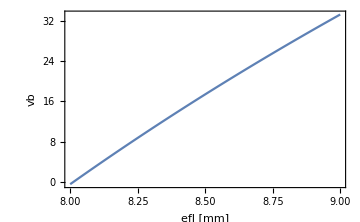

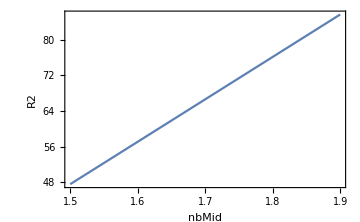

```mathematica
ftot = 8.75;
r1 = 6.215;  (*6.215 is RoC of edmund 10mm 0.63 NA asphere*)
(*N-LAF21, the crown*)
na=Interpolation[Transpose@{{643.8,656.3,706.5,852.1,1014,1060},{1.78380,1.78301,1.78019,1.77434,1.76995,1.76892}}];
naL1 = na[780];
naL2 = na[852];
naMid = (naL1+naL2)/2 ;
va = (naMid -1)/(naL1 - naL2);

(*find the flint we need*)
"required Flint Abbe number"
vb=va(1-r1/(ftot (naMid-1)))
Plot[va(1-r1/(efl (naMid-1))), {efl,8,9},FrameLabel->{"efl [mm]","vb"}]
Plot[ ftot (va-vb)/vb(nbMid-1),{nbMid,1.5,1.9},FrameLabel->{"nbMid","R2"}]
```

```mathematica
(*N-LAK22 for the flint.*)
nb=Interpolation[Transpose@{{643.8,656.3,706.5,852.1,1014,1060},{1.64816,1.64760,1.64560,1.64141,1.63823,1.63747}}];
(*N-SF6 for the flint.*)
(*nb=Interpolation[Transpose@{{643.8,656.3,706.5,852.1,1014,1060},{1.79749,1.79608,1.79114,1.78144,1.77486,1.77341}}];
*)
nbL1 = nb[780];
nbL2 = nb[852];
nbMid = (nbL1+nbL2)/2;
"Flint Abbe number"
vb = (nbMid -1)/(nbL1 - nbL2)
"RoC 2"
r2 = ftot (va-vb)/vb(nbMid-1)
```

Flint Abbe number

348.305

RoC 2

-0.724077

```mathematica
(1.74895+1.86506)/2-1
```

RoC 2

4.16112

different approach. pick a reasonable Abbe number, then solve for R2(nbMid). Plot then find glass with similar mean index of refraction.

```mathematica
Clear[va,vb,nbMid,ftot]
```

```mathematica
r1 = ftot (va-vb)/va(naMid-1)
"RoC 2"
r2 = ftot (va-vb)/vb(nbMid-1)
```

```mathematica
Solve[r2 == ftot (va-vb)/vb(nbMid-1),vb]
```

{{vb→(ftot (-1+nbMid) va)/(-ftot+ftot nbMid+r2)}}

```mathematica
Solve[r2==ftot (va-((ftot (-1+nbMid) va)/(-ftot+ftot nbMid+r2)))/((ftot (-1+nbMid) va)/(-ftot+ftot nbMid+r2)),r2]
```

{{r2→0}}

```mathematica
r2==ftot (va-((ftot (-1+nbMid) va)/(-ftot+ftot nbMid+r2)))/((ftot (-1+nbMid) va)/(-ftot+ftot nbMid+r2))//FullSimplify
```

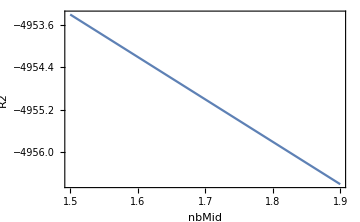

```mathematica
Plot[ (ftot va+ftot vb-ftot nbMid vb)/vb,{nbMid,1.5,1.9},FrameLabel->{"nbMid","R2"}]
```

## triplet

### custom thin triplet

```mathematica
{K == K1+h2/h1 K2+h3/h1 K3, 
P==K1/n1+K2/n2+K3/n3,
C1 = h1^2/v1+h2^2}
```

K

## designed lens performance

### high NA asphere + thicker corrective doublet + 820 + fiber cpl check_hammered.zmx

Move the 0.54 NA source in and out of focus and see the effect on fiber coupling efficiency.

```mathematica
coupling = {0.016, 0.038,0.055,0.05,0.024,0.013,0.072, 0.235,0.473,0.69,0.778,0.519,0.471,0.231,0.069,0.01,0.015,0.027,0.02,0.008,0.012};
defocus = Range[-10,10,1];
```

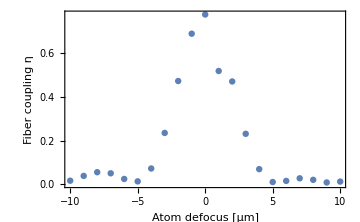

```mathematica
ListPlot[Transpose@{defocus,coupling}, FrameLabel->{"Atom defocus [μm]","Fiber coupling η"}]
```

### high NA asphere + thicker corrective doublet + 820 + fiber cpl check global_best_20210824.zmx

Move the 0.54 NA source in and out of focus and see the effect on fiber coupling efficiency.

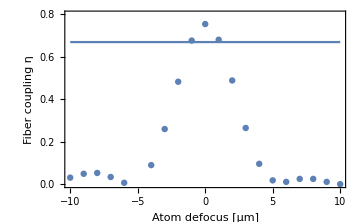

```mathematica
coupling = {0.031,0.049,0.053,0.034,0.006647,0011,0.09,0.260,0.483,0.677,.755,0.681,.489,.265,0.096,0.018,0.011,0.025,0.025,0.011,0.0002347};
defocus =Range[-10,10,1];
Show[
ListPlot[Transpose@{defocus,coupling}, FrameLabel->{"Atom defocus [μm]","Fiber coupling η"},PlotRange->{0,0.8}],
Plot[.67,{x,-10,10}]]
```

```mathematica
10+7.9+6.3+2.9+3.7+5.9
```

36.7

```mathematica
(.85)/(π Tan[ArcSin[0.13]])
```

2.0636

```mathematica
ArcSin[0.13]180/π
```

7.46959

```mathematica
(π 2.2^2)/0.82
```

18.5431

## Axes for my OpticStudio universal plots

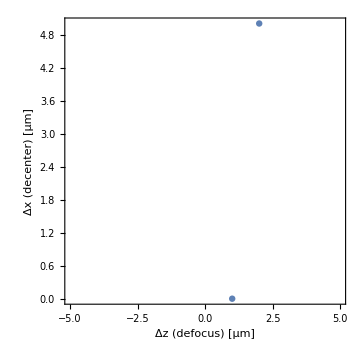

```mathematica
ListPlot[{0,5},PlotRange->{{-5,5},{0,5}},AspectRatio->1, FrameLabel->{"Δz (defocus) [μm]","Δx (decenter) [μm]"}]
```

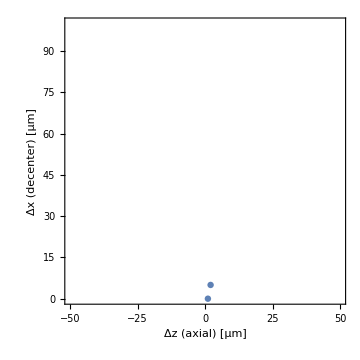

```mathematica
ListPlot[{0,5},PlotRange->{{-50,50},{0,100}},AspectRatio->1, FrameLabel->{"Δz (axial) [μm]","Δx (decenter) [μm]"}]
```

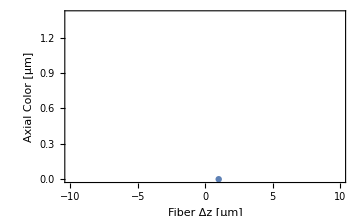

```mathematica
ListPlot[{0,5},PlotRange->{{-10,10},{0,1.4}},AspectRatio->.6, FrameLabel->{"Fiber Δz [μm]","Axial Color [μm]"}]
```